## Section | Dissipative interactions and open quantum systems

The chapter begins by discussing the concept of decoherence and dissipation, emphasizing that while the evolution of isolated quantum systems is unitary and preserves coherence, real-world systems are rarely isolated. We describe the mathematical formalism of open quantum systems, the role of the density matrix in describing mixed states, and the master equation approach to modeling decoherence dynamics. The chapter also explores specific examples, such as the decoherence of superposition states (e.g., Schrödinger cat states) and other phenomena that can be described by master equations.

### Key concepts

Lindblad master equation

Decoherence

Modeling open quantum systems

QuantumOperator + QuantumEvolve workflow for master equations

## Quantum jump approach and decoherence

Quantum theory was initially developed as a theory based on ensembles because it was thought that manipulating single quantum systems (like one electron or one atom) was impossible. In 1975 Dehmelt proposed in the context of fluorescence spectroscopy some schemes for measuring transition frequencies that required single quantum system observations, that were later implemented using single ion traps. Predictions were confirmed by experiments that impulsed the development of the quantum jump approach

### Algorithm for general quantum jump

The quantum jump method is similar to Monte Carlo methods, and we assume a cavity field at T = 0 K and a photon emission means the field loses one photon represented by an annihilation operator

Calculate the current probability ΔP of emission of a photon in a time interval δt according to  where is one member of the ensemble

Obtain a random number 0 ≤ r < 1, compare with ΔP to decide emission

Emit if r < ΔP (field loses one photon), the system jumps to renormalized form

No emission r > ΔP, the system evolves according to


where  is the effective non Hermitian Hamiltonian describing non unitary evolution where the second term represents decay of the cavity field.

Iterate the process to record a trajectory of conditional evolution of one member of the ensemble with jump events  t_(1,)t_2...

Average observables over a big number of trajectories to get average behavior or whole ensemble

### Master equation for density operators

The history of a particular trajectory splits into two alternatives in a time Δt to allow at most one jump, either it jumps or it does not

For a pure state  the evolution can be described as a sum of two outcomes:

Averaging  over all the members of the ensemble:

Taking the limit as δt → 0 we get a differential equation

Referred as the master equation which can also be obtained from more complicated methods for the T = 0 K damping problem

### Quantum jumps on familiar states

Assuming no interaction (Ĥ = 0) so only the dissipation acts. If we have an initial cavity field in a coherent state |α⟩ the jump evolution leaves the field unchanged because a coherent state is eigenstate of the annihilation operator, and the no jump-evolution results:

Set truncation size:

```mathematica
SetFockSpaceSize[20];
```

Term describing non unitary evolution:

```mathematica
Hdisp = - ⅈ h (γ/2) SuperDagger[a]@a;
```

We will verify the no-jump evolution symbolically.  We get a valid relation because the square root in the denominator  just a normalizing factor, quantum state equality in Wolfram QuantumFramework work up to global phases and multiplicative factors.

Symbolic comparison:

```mathematica
MatrixExp[- ⅈ Hdisp /h δt] @ CoherentState[][α]  == CoherentState[][α ⅇ^(-γ δt /2)]
```

True

The coherent state remains a coherent state after the evolution, however, the amplitude of the state has an exponential decay due to the non unitary Hamiltonian

Non-unitary Hamiltonian:

```mathematica
Hdisp["UnitaryQ"]
```

False

If we now consider the cavity field is prepared in a even cat state  where 𝒩_e   is  a normalization constant , the annihilation operator converts an even cat state to odd cat state

Photon distribution corresponds to odd cat state after jump:

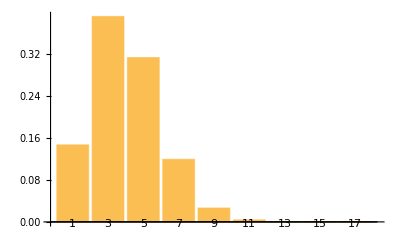

```mathematica
(a @ CatState[][2.,0])["ProbabilityPlot"]
```

For a no jump transition the field state decays referred as “jumping-cat” transition

Since we will also verify this symbolically we will work without normalizing, that is why we wont use CatState (which comes Normalized). Instead we just define the superposition of non normalized coherent states

Coherent state superposition:

```mathematica
evenCat = QuantumState[CoherentState[][α]+CoherentState[][-α],"Parameters"->α];
```

“No-jump” evolution:

```mathematica
MatrixExp[- ⅈ Hdisp /h δt] @ evenCat  == evenCat[α ⅇ^(-γ δt /2)]
```

True

The cat state “reduce”  during no-jump evolution (the amplitude decays)

### Decoherence

It can be defined as transformation over time of a quantum mechanical superposition into a classical statistical mixture, as a result of interaction with an environment. As an example, consider  an initial even cat state , the cavity-environment state is

where |ϵ ⟩ is the quantum state of the environment. The environment can be described  with an arbitrary number of systems and states which are not relevant for the analysis. At a later time the system will evolve to

with    from the earlier section so that the field becomes entangled with the environment. If we compute the density operator and trace over a complete set of states of the environment , we get a reduced field density operator

is a statistical mixture of two coherent states

## Dissipative interactions from master equations

### Dissipation of a coherent state

```mathematica
SetFockSpaceSize[15];
```

Initial parameters for a coherent state |α⟩ , α with amplitude equal to 2:

```mathematica
αcoh = 2*Exp[I RandomReal[{0,2Pi}]];
ρ0=coherent[αcoh];
```

Establishing a damping parameter:

```mathematica
γ = RandomReal[{1,2}];
```

Setting up the Liouvillian master equation with Ĥ=(â)^†â and L_1 = â:

```mathematica
ℒ= QuantumOperator["Liouvillian"[SuperDagger[a]@a,{a},{γ}]];
```

ℒ is a superoperator:

```mathematica
ℒ["Type"]
```

Superoperator

Computing the evolution numerically:

```mathematica
ρt=QuantumEvolve[I ℒ,ρ0,{t,0,1}];
```

Extra variables for computing the evolution statistics:

```mathematica
time=Range[0,1,0.01];
fock=Range[$FockSize]-1;
```

Computing mean number of photons and the fidelity with respect to an analytical solution:

```mathematica
qs=QuantumSimilarity[coherent[αcoh ⅇ^(-ⅈ #) ⅇ^(-1/2 # γ)],ρt[#]]&/@time;
meanN=Chop[fock.Diagonal[ρt[#]["DensityMatrix"]]]&/@time;
```

Plotting the statistics, the evolved state behaves like a coherent state that decays in amplitude:

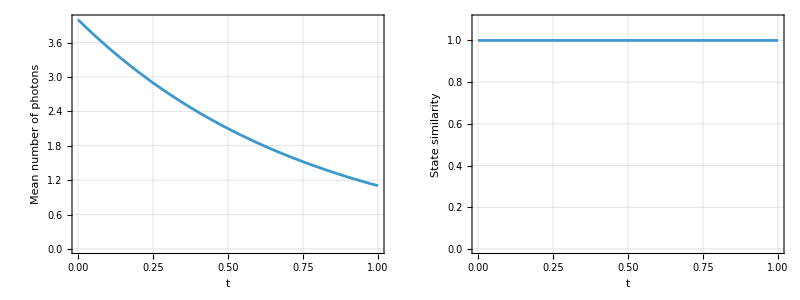
-Graphics-Evolution statistics of a coherent state

```mathematica
Labeled[Grid[{{ListLinePlot[Thread[{time,meanN}],],ListLinePlot[Thread[{time,qs}],]}}],]
```

|α|^2exp(-γt) function represents what was obtained . The decay time of the field energy is

Do an exponential decaying fit:

```mathematica
nlm =NonlinearModelFit[Thread[{time,meanN}],k Exp[-g t],{k,g},{t}]
```

FittedModel[…]

Compare the parameters:

```mathematica
(g /. nlm["BestFitParameters"]) - γ
```

2.82429×10^-8

Spiral motion of the center of the Wigner representation of the coherent state, the Hamiltonian with unit frequency makes the coherent state rotate, and the dissipation  makes it go towards the origin:

-Graphics- | -Graphics-
-Graphics- | -Graphics-

### Decoherence of an even cat : becoming statistical mixture

```mathematica
SetFockSpaceSize[15];
```

Now we analyze the evolution of  a cavity prepared with an even cat state:

```mathematica
αcoh = 2*Exp[I RandomReal[{0,2Pi}]];
ρ0 = CatState[][αcoh,0];
```

Setting a pure decoherence master equation with photon loss (H = 0):

```mathematica
γ = 0.9;
ℒ= QuantumOperator["Liouvillian"[None,{a},{γ}]];
```

Evolving the state:

```mathematica
ρt = QuantumEvolve[ⅈ ℒ, ρ0, {t,0,10}];
```

Monitoring how the traces change. is related to the purity and also a measure of decoherence. But there will be a point that purity starts to increase because the decay in energy makes the state to start to get similar to the vacuum (pure state) :

Sampling time:

```mathematica
time=Range[0,10,0.01];
```

Compute traces:

```mathematica
traces = Table[{Tr[ρt[t]],ρt[t]["Purity"]},{t,time}];
```

Plot result:

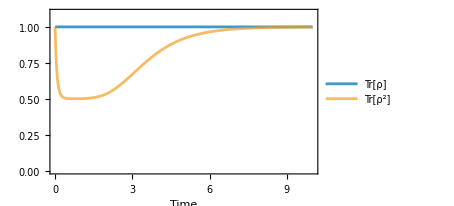

```mathematica
ListLinePlot[{Thread[{time,traces[[All,1]]}],Thread[{time,traces[[All,2]]}]},]
```

The energy decay (mean photon number) still decays exponentially as expected :

```mathematica
meanPhotons = Table[{t,Dot[fock,Diagonal[ρt[t]["DensityMatrix"]]]},{t,time}] ;
```

Plot the curve:

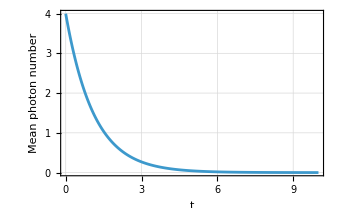

```mathematica
ListLinePlot[meanPhotons,]
```

The theoretical solution of the master equation  is:

Implement analytical solution:

```mathematica
sol =QuantumState[coherent[αcoh ⅇ^(-γ  t/2)]["MatrixState"]+coherent[-αcoh ⅇ^(-γ  t/2)]["MatrixState"]+ QuantumOperator[ⅇ^(-2 Abs[αcoh]^2(1-ⅇ^(-γ t)))(coherent[αcoh ⅇ^(-γ  t/2)]@SuperDagger[coherent[-αcoh ⅇ^(-γ t /2)]]+coherent[-αcoh ⅇ^(-γ  t/2)]@SuperDagger[coherent[αcoh ⅇ^(-γ t /2)]])]["MatrixQuantumState"],"Parameters"->t]["Normalize"];
```

Compute fidelities:

```mathematica
AbsoluteTiming[similarities = Table[QuantumSimilarity[ρt[t],sol[t]],{t,0,10,0.05}];]
```

{34.4761,Null}

Verifying are the same(basically 1 with  numerical error):

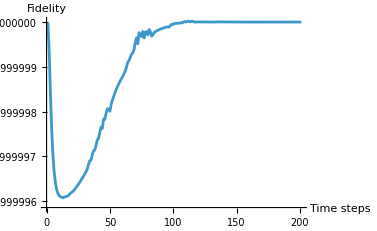

```mathematica
ListLinePlot[similarities,AxesLabel->{"Time steps","Fidelity"}]
```

Apart  from the energy decay we can see there is another quantity the decays from the theoretical solution multiply the “coherences”(off diagonal elements). For short times a decoherence time is obtained from expansion .  as long as .

This can be visualized with the Wigner representation, using some time in between T_decay and T_decoh:

```mathematica
Tevol = 1/(2γ);
```

Statistical mixture:

```mathematica
ρmix = 1/2(coherent[αcoh]["MatrixState"]+coherent[-αcoh]["MatrixState"]);
```

Plot Wigner function:

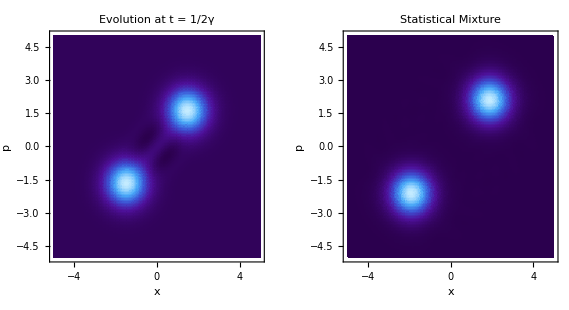

```mathematica
GraphicsRow[Table[wig = WignerRepresentation[s[[1]],{-5,5},{-5,5}];DensityPlot[wig[x,p],{x,-5,5},{p,-5,5},],{s,{{ρt[Tevol],"Evolution at t = 1/2γ"},{ρmix,"Statistical Mixture"}}}],Spacings->20]
```

This verifies the “coherences” decay faster than the energy and the states becomes a statistical mixture, of course the amplitude is not the same because during the evolution  photon loss has acted

But after a long time, the photon loss is big enough that the state becomes the vacuum:

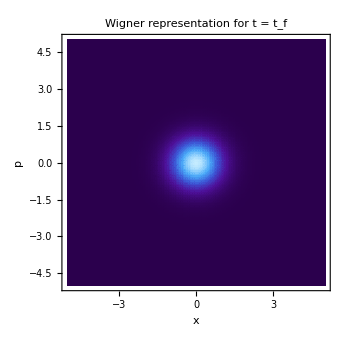

```mathematica
wig = WignerRepresentation[ρt[10.],{-5,5},{-5,5}]; DensityPlot[Chop@wig[x,p],{x,-5,5},{p,-5,5},]
```

## Generation of coherent states from decoherence: optical balance

Dissipation destroy coherence in quantum superposition effects. However, even if it does not sound intuitive, it is also possible to create coherence from dissipative effects. The master equation has unitary(the commutator)and non-unitary terms(dissipation) with nonlinear behavior in the creation and annihilation operators. The interactions can “balance each other” such that the evolution at t → ∞  is  a different state than the vacuum.

Considering an interaction Hamiltonian OverHat[H_I] = h G(â+(â)^†)  where G is the strength of a classical pump field that propagates in a photon absorbing medium (dissipation). The master equation becomes:

We start with a random cavity field:

```mathematica
ρ0 = QuantumState["RandomPure",$FockSize]
```

QuantumState[…]

Establishing simulation parameters, driving strength and photon loss rate:

```mathematica
G = RandomReal[{1,2}];
γ  = RandomReal[{1.5,2}];
```

Liouvillian of the master equation now we consider a driving interaction term  Ĥ ≠ 0:

```mathematica
ℒ= QuantumOperator["Liouvillian"[G(a+SuperDagger[a]),{a},{γ}]];
```

Solving the master equation:

```mathematica
ρt =QuantumEvolve[ ⅈ ℒ,ρ0,{t,0,3}];
```

The steady-state solution of the equation converges to ρ = |β ⟩ ⟨β| where β = - 2 ⅈ G/γ:

```mathematica
similarities= Table[{t,QuantumSimilarity[ρt[t],coherent[-I 2G/γ]]},{t,0,3,0.1}];
```

Plot state-fidelity, we see it approaches 1 as time evolves:

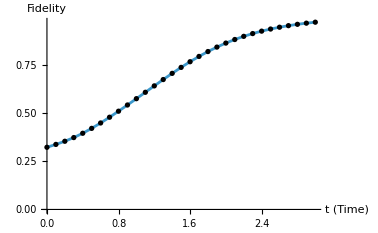

```mathematica
ListLinePlot[similarities,]
```

If we have an initial vacuum state  ρ̂(0) = |0⟩ ⟨0| at short times enough to ignore dissipation. The evolution will be unitary and we will get a coherent state  of the form | -ⅈ G t ⟩⟨- ⅈ G t | independent of γ . Fidelity remains around 1 for small times until the approximation is no longer valid

Evolving the ground state:

```mathematica
ρt =QuantumEvolve[ ⅈ ℒ,FockState[0],{t,0,3}];
```

Auxiliary variables for time steps and Fock numbers:

```mathematica
time = Range[0,0.8,0.02];
fock =Range[$FockSize]-1;
```

Computing fidelities and mean photon number:

```mathematica
qs = QuantumSimilarity[coherent[-I G #],ρt[#]]& /@ time;
meanN = Chop[fock.Diagonal[ρt[#]["DensityMatrix"]]]& /@ time ;
```

Plot the statistics:

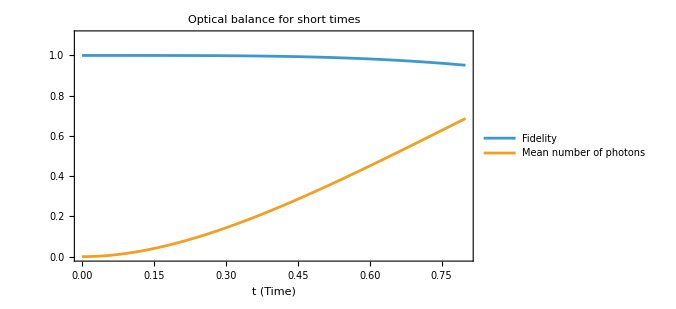

```mathematica
ListLinePlot[{Thread[{time,qs}],Thread[{time,meanN}]},]
```

## Thermalization master equation

Master equation:

where n_th is the thermal photon number that is dependent on temperature and frequency of the cavity, and κ is the decay photon rate

Set up truncation size:

```mathematica
SetFockSpaceSize[25];
```

Final time:

```mathematica
tf = 10.;
```

Setting the master equation (Ĥ = ℏ ω a^†a) with the relevant jump operators:

```mathematica
ℒ = QuantumOperator["Liouvillian"[ ω SuperDagger[a]@a,{a,SuperDagger[a]},{κ(nth+1),κ nth}],"Parameters"->{ω,κ,nth}];
```

Pick some parameters, for example n_th = 3, ω = 1, κ = 0.6 :

```mathematica
liouville =ℒ[1,0.6,3];
```

Calculating mean number of photons for different initial Fock states:

```mathematica
meanPhotons =
Table[ρt = QuantumEvolve[ⅈ liouville ,FockState[i],{t,0,tf}];Table[{t,Dot[Range[0,$FockSize-1],Diagonal[ρt[t]["DensityMatrix"]]]},{t,0,tf,0.01}],{i,{0,1,4}}];
```

Plot mean number of photons, see the convergence towards 3:

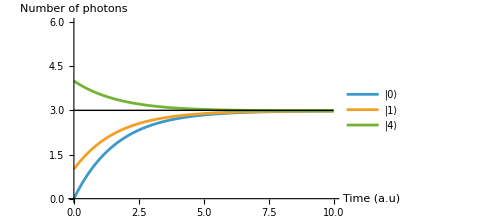

```mathematica
ListLinePlot[meanPhotons,]
```

It indeed converges to a thermal state:

```mathematica
QuantumSimilarity[ρt[tf],ThermalState[3.]]
```

0.999624

Changing the κ parameter, compute evolved states:

```mathematica
evolved =Table[QuantumEvolve[ⅈ ℒ[1,k,3],FockState[0],{t,0,tf}],{k,{0.5,1.,1.5}}];
```

Calculate again the mean number of photons:

```mathematica
meanPhotons =Table[{t,Dot[Range[0,$FockSize-1],Diagonal[#[t]["DensityMatrix"]]]},{t,0,tf,0.01}]&/@evolved;
```

Plot the curves, we see change in the rate of convergence such that higher κ converges faster:

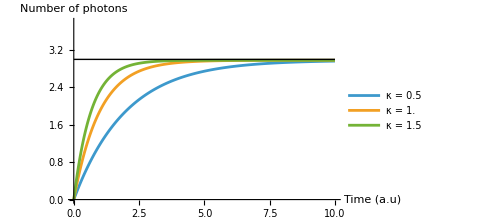

```mathematica
ListLinePlot[meanPhotons,]
```

Paclet installation

Install  the Quantum Framework paclet:

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
PacletObject[…]
```

Load quantum framework functions:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load quantum framework functions for the second quantization:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Useful definitions:

```mathematica
a := AnnihilationOperator[]
coherent := CoherentState[]["Normalize"]
```